## Grover Search Algorithm

```mathematica
<<Wolfram`QuantumFramework`
```

### Key Concepts

Boolean function

Asymptotic advantage

### Statement of the Grover Search Problem

In the last lesson, you saw a quantum algorithm for solving the Bernstein-Vazirani problem. A similar problem is known as the Grover search problem. This problem can be stated as follows:

There is a secret integer ω somewhere in the domain {0,…,n-1}.

There is an oracle function, f, with domain {0,…,n-1} and range {0,1}. This function outputs 1 if and only if the input is the secret integer. The output is 0 otherwise. Formally, f:{0,…,n-1}↦{0,1} such that f(x)=Piecewise[{{1, x==ω}, {0, x!=ω}}].

There is an oracle subroutine, U_ω, which acts on indexed quantum states as U_ω x=(-1)^(f(x))x.

The goal is to guess the secret integer, ω, with as few uses of the oracle subroutine as possible.

### Classical Version

The classical version of the problem amounts to “can you guess the number?” If there are n possibilities, then your first guess will only be correct with probability 1/n. However, on your second guess, you should not repeat your first guess (since you will already know the status of your first guess). Thus, the probability to guess correctly will be 1/(n-1) on the second guess. After you guess n-1 times, you are certain to know the secret number. Either you will have guessed the correct number or you will have eliminated all incorrect options.

You could summarize the success chance of this “classical search” as P_success(k)=(k+1)/n where k is the number of times you use the oracle function.

As an example, suppose the secret number is between 0 and 7, inclusive (in other words, there are 2^3 possibilities). Then, there will be at most 7 oracle queries needed to be certain of the secret number.

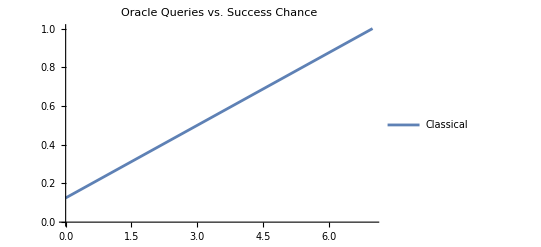

```mathematica
ListPlot[Table[{k,(k+1)/8},{k,0,7}],Joined->True,PlotLabel->"Oracle Queries vs. Success Chance",PlotLegends->{"Classical"}]
```

### Grover’s Algorithm

In the quantum version of the algorithm, one first encodes the problem in qubits. Consider the prior example where the secret number is between 0 and 7, inclusive. Suppose for the example that the secret number is 5. A straightforward encoding of the problem would require 3 qubits since there are 2^3 possible numbers. The state corresponding to the secret number would then be 101, or 5 in binary representation.

Similar to the Bernstein-Vazirani algorithm, Grover’s search algorithm uses an oracle that depends on the secret number. To construct the oracle, you will need 1 additional qubit and a CNOT gate with the first 3 qubits as controls. This CNOT gate will be equivalent to a Boolean function that flips the additional qubit if and only if the controls encode the secret number. The phase kickback from this CNOT gate implements the oracle subroutine U_ω.

Since the secret number in this example is encoded by the state 101, the needed boolean function can be given by:

```mathematica
bf=BooleanFunction[{{True,False,True}->True,{__}->False},{a,b,c}]
```

a&&!b&&c

You can check this is the correct boolean function because the binary string “101” satisfies the relationship.

```mathematica
SatisfiabilityInstances[bf,{a,b,c}]//Boole
```

{{1,0,1}}

The CNOT gate which implements U_ω is then:

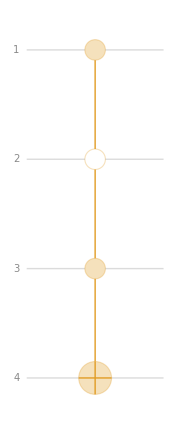

```mathematica
QuantumCircuitOperator["BooleanOracle"[bf]]["Diagram",ImageSize->Small]
```

Unlike the Bernstein-Vazirani oracle, there is an additional operation required to use this oracle in the circuit. The full Grover search operation looks like this:

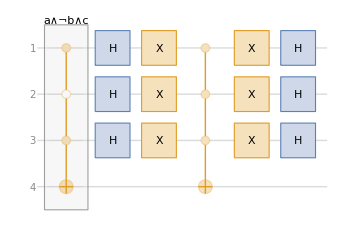

```mathematica
gs=QuantumCircuitOperator["Grover"[bf]];
gs["Diagram"]
```

The second block of gates is known as the Grover diffusion operator. The combination of the Boolean oracle and Grover diffusion operator are applied together in one iteration of the algorithm. To take advantage of the phase kickback introduced by the controlled gates, the circuit will need an initial set of gates and finally a measurement of the first three qubits.

One iteration of the Grover algorithm for the current example would look like this:

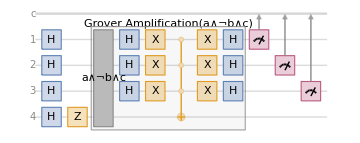

```mathematica
oneIteration=QuantumCircuitOperator[{Splice@Thread["H"->Range[4]],"Z"->4,gs,Splice@Thread["M"->Range[3]]}];
oneIteration["Diagram"]
```

The measurement distribution for this circuit is shown below:

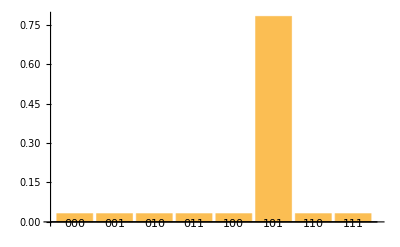

```mathematica
oneIteration[]["ProbabilitiesPlot"]
```

Notice how the secret number (encoded in binary as “101”) is the most likely result.

Each iteration of the so-called Grover operator uses the oracle subroutine once. What happens if two iterations are used instead of one?

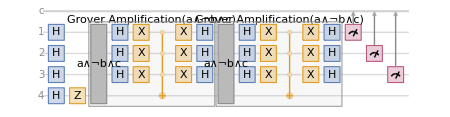

```mathematica
twoIteration=QuantumCircuitOperator[];
twoIteration["Diagram",ImageSize->450]
```

The circuit is longer, but now the probability for obtaining the desired outcome is increased:

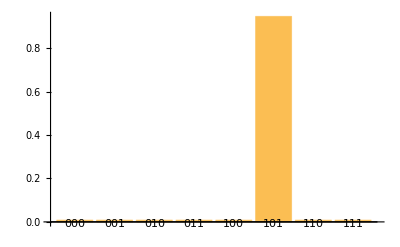

```mathematica
twoIteration[]["ProbabilitiesPlot"]
```

Since the classical search needs at most 7 iterations, compute the quantum states after 0 to 7 iterations of the Grover algorithm:

```mathematica
ψ0=QuantumState["+++-"];
states=NestList[gs,ψ0,7];
```

Next, look at the probability plots for each of these states when measured:

```mathematica
TabView@MapThread[#2->QuantumMeasurementOperator[{1,2,3}][#1]["ProbabilitiesPlot",PlotRange->{0,1},PlotRangePadding->Scaled[.1],PlotLabel->StringJoin["Grover Iterations: ",ToString@#2,"\nSecret: ",ToString@{1,0,1}]]&,{states,Range[Length@states]-1}]
```

12345678

As you can see, the probability rises then falls and rises again as more and more Grover iterations are applied.

However, the probability of success has an initial increase that is substantially greater than in the classical case:

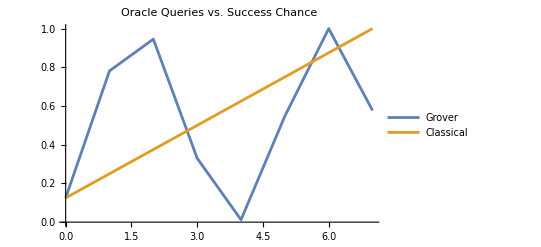

```mathematica
With[
{
grover=Table[{k,QuantumMeasurementOperator[{1,2,3}][states[[k+1]]]["Probabilities"][[6]]},{k,0,7}],
classical=Table[{k,(k+1)/8},{k,0,7}]
},
ListPlot[{grover,classical},Joined->True,PlotLegends->{"Grover","Classical"},PlotLabel->"Oracle Queries vs. Success Chance"]
]
```

Although details are beyond the scope of the course, it can be shown that the success chance after r repetitions of the Grover operator to find one number out of n possibilities is given by the expression: sin^2((2 r+1) sin^-1(1/(√n)))

```mathematica
success=Sin[(2r+1)ArcSin[1/Sqrt[n]]]^2
```

Sin[(1+2 r) ArcSin[1/(√n)]]^2

This is exactly the pattern you observed in the last plot:

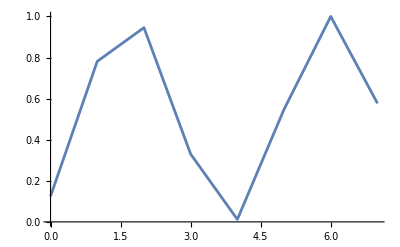

```mathematica
ListPlot[Table[{r,success/.n->8},{r,0,7}],Joined->True]
```

Since n is fixed for any given Grover search problem, the success chance is periodic, rising and falling as more iterations are applied:

```mathematica
FunctionPeriod[success,r]
```

π/(2 ArcSin[1/(√n)])

When does the probability for success approach 1?

```mathematica
SolveValues[success==1,r]
```

{ConditionalExpression[(-π/2-ArcSin[1/(√n)]+2 π C[1])/(2 ArcSin[1/(√n)]), C[1]∈ℤ],ConditionalExpression[(π/2-ArcSin[1/(√n)]+2 π C[1])/(2 ArcSin[1/(√n)]), C[1]∈ℤ],ConditionalExpression[((3 π)/2-ArcSin[1/(√n)]+2 π C[1])/(2 ArcSin[1/(√n)]), C[1]∈ℤ]}

When any of the these expressions are close to an integer, the success probability for the Grover algorithm will be high. What is the behavior of this expression as n becomes very large?

```mathematica
Asymptotic[(π/2-ArcSin[1/(√n)])/(2 ArcSin[1/(√n)]),n->Infinity]
```

(√n π)/4

Recall how the number of oracle queries needed for the classical algorithm grew at the same rate as the size of the search space, n. Grover’s search provides an example of asymptotic advantage for a quantum algorithm. The O(√n) iterations needed for the quantum algorithm grows more slowly than the O(n) iterations needed for the classical algorithm. Thus, for large problems, the quantum algorithm requires fewer iterations.